## Functions for computations

Remember to run the following cell before the computations.

```mathematica
(* Compute line between the points {x1,y1} and {x2,y2} *)
line[{x1_,y1_},{x2_,y2_}]:=If[x1 -x2!=0, (y2-y1)/(x2-x1)*x-y+(y2- (y2-y1)/(x2-x1)*x2),x-x1];


(* See if line l supports the polygon with vertices a1,a2,a3,a4 returns True or False *)
supp[l_, a1_,a2_,a3_,a4_]:=
Module[{vals},vals=Block[{x,y},
{l/. {x->a1[[1]],y->a1[[2]]},
l/. {x->a2[[1]],y->a2[[2]]},
l/. {x->a3[[1]],y->a3[[2]]},
l/. {x->a4[[1]],y->a4[[2]]}}];
Simplify[(And@@Thread[vals>=0])||(And@@Thread[vals<=0])]
]

(* Given outer vertex q and inner vertices p1,p2,p3,p4, find the two lines q-pi and q-pj such that the lines q-pi and q-pj support the polygon with the inner vertices, returns list with the lines that are supporting the inner polygon *)
findSupportingLines[q_,a1_,a2_,a3_,a4_]:=Module[{l1,l2,l3,l4,supportingLines},
l1=line[q,a1];
l2=line[q,a2];
l3=line[q,a3];
l4=line[q,a4];
supportingLines={};
If[l1 =!= Nothing &&supp[l1,a1,a2,a3,a4],AppendTo[supportingLines,l1]];
If[l2 =!= Nothing &&supp[l2,a1,a2,a3,a4],AppendTo[supportingLines,l2]];
If[l3 =!= Nothing &&supp[l3,a1,a2,a3,a4],AppendTo[supportingLines,l3]];
If[l4 =!= Nothing &&supp[l4,a1,a2,a3,a4],AppendTo[supportingLines,l4]];
Return[supportingLines];
];

(* Find the intersection of line l with boundary defined by s1,s2,s3,s4. Returns the intersection point v={x,y} that is not the point q *)
findIntersectionWithBoundary[l_,s1_,s2_,s3_,s4_,ineqsQ_,q_]:=Module[{linesToCheck,solsubs,v}, 
linesToCheck={s1,s2,s3,s4};
For[i=1,i<=Length[linesToCheck],i++, solsubs= Solve[l==0 && linesToCheck[[i]]==0 &&ineqsQ, {x,y},Reals]; If[solsubs =!= {}, 
v = {x,y}/.solsubs[[1]]; 
If[v[[1]]!= q[[1]] ||v[[2]]!=q[[2]], Return[v]]
];
];
Nothing
];

(* Check if inner polygon is contained in triangle. INPUT: the edges of triangle and inner vertices. Checks if edges of triangle support inner polygon. Returns True or False *)
isContained[l1v1_,l1v2_ ,lv1v2_,a1_,a2_,a3_,a4_]:=
Module[{res},res=supp[l1v1,a1,a2,a3,a4]&&supp[l1v2,a1,a2,a3,a4]&&supp[lv1v2,a1,a2,a3,a4];
If[res == True,Print["True: This is a triangle nested in between P and Q."],Print["False: This triangle is not nested between P and Q"]];
Return[res] 
]

(*Intersection point of the lines l1 and l2*)
point[l1_,l2_]:=Module[{sol},
sol = Solve[l1==0&&l2==0,{x,y}, Reals];
If[sol=!= {},{x,y}/.sol[[1]], Nothing]
]

(* Find the two intersection points of the line l with the boundaries s1,s2,s3,s4, satisfying the inequalities defined by ineqsQ. Returns list of intersection points vi = {xi,yi} *)
findIntersectionWithBoundaryTwoPoints[l_,s1,s2,s3,s4,ineqsQ]:= Module[{linesToCheck,intersections, v,vsubs,res},
linesToCheck={s1,s2,s3,s4};
intersections={};
For[i=1,i<=Length[linesToCheck],i++,
v=point[l,linesToCheck[[i]]];
vsubs= {x->v[[1]],y->v[[2]]};
res = Reduce[ineqsQ/.vsubs];
If[res==True, AppendTo[intersections, v]]
];
Return[intersections]
];

(* Given vertex v, find out whether the line v--innerv1 or v--innerv2 supports the polygon with vertices a1,a2,a3,a4. Returns the line l that supports the polygon. *)
findSupportingVertex[v_,innerv1_,innerv2_ ,a1_,a2_,a3_,a4_]:=Module[{innervertices,l},
innervertices = {innerv1,innerv2};
For[i=1,i<=Length[innervertices],i++,
l = line[v,innervertices[[i]]];
If [supp[l,a1,a2,a3,a4] == True, Return[l]]
]
];
```

## Example 5.9

### Define partial matrix and find rank-3 completion

```mathematica
Mm={{x,1,112/425,1},{1/10,b1,1/100,7/20},{1/10,10,9/10,3/5},{4/5,9,9/100,1/20}};
A = {{a11,a12,a13},{1,0,0},{0,1,0},{0,0,1}};
B = {{1/10,b1,1/100,7/20},{1/10,10,9/10,3/5},{4/5,9,9/100,1/20}};
```

```mathematica
sol1 = Solve[(A.B)[[1,{3,4}]]==Mm[[1,{3,4}]],{a11,a12}];
A2 = A/.sol1[[1]]
```

{{(4204+51 a13)/1751,(1398-527 a13)/5253,a13},{1,0,0},{0,1,0},{0,0,1}}

```mathematica
sol2=Solve[(A2.B)[[1,2]]==Mm[[1,2]],a13];
A3 = A2/.sol2[[1]]//Simplify
```

{{100601/(42007+153 b1),(12055+1306 b1)/(42007+153 b1),-(3 (2909+4204 b1))/(17 (2471+9 b1))},{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Mm = A3.B//Simplify;
Mm//MatrixForm
```

((4284-9959 b1)/(42007+153 b1) | 1 | 112/425 | 1
1/10 | b1 | 1/100 | 7/20
1/10 | 10 | 9/10 | 3/5
4/5 | 9 | 9/100 | 1/20)

```mathematica
(*Find bounds for nonnegativity *)
boundsforM  = Reduce[Mm>=0,b1]
```

0≤b1≤4284/9959

### Define polytopes

```mathematica
(* Define inner polytope P by taking slice x+y+z=1 *)
B1 = B[[All,1]];
B2=B[[All,2]];
B3 =  B[[All,3]];
B4 =  B[[All,4]];
l1sol = Solve[l1*(B1[[1]]+B1[[2]]+B1[[3]])==1,l1];
p1 = l1*B1/.l1sol[[1]];
l2sol = Solve[l2*(B2[[1]]+B2[[2]]+B2[[3]])==1,l2];
p2 = l2*B2/.l2sol[[1]];
l3sol=Solve[l3*(B3[[1]]+B3[[2]]+B3[[3]])==1,l3];
p3 = l3*B3/.l3sol[[1]];
l4sol = Solve[l4*(B4[[1]]+B4[[2]]+B4[[3]])==1,l4];
p4 = l4*B4/.l4sol[[1]];

(* Vertices of P *)
p1= {p1[[1]],p1[[2]]}
p2= {p2[[1]],p2[[2]]}
p3= {p3[[1]],p3[[2]]}
p4= {p4[[1]],p4[[2]]}
```

{1/10,1/10}

{b1/(19+b1),10/(19+b1)}

{1/100,9/10}

{7/20,3/5}

```mathematica
(* Define outer polytope Q by taking slice x+y+z=1 *)
ineqsQ=And@@Thread[(#.({x,y,-x-y+1})>=0)&/@A3]

BoundariesQ= A3.{x,y,-x-y+1};
{s1,s2,s3,s4}=BoundariesQ;
```

(100601 x)/(42007+153 b1)-(3 (2909+4204 b1) (1-x-y))/(17 (2471+9 b1))+((12055+1306 b1) y)/(42007+153 b1)≥0&&x≥0&&y≥0&&1-x-y≥0

```mathematica
ineqsQ0 = ineqsQ/.{b1->boundsforM[[1]]};
q01= point[s1,s3]/.{b1->boundsforM[[1]]};
q02 = point[s1,s2]/.{b1->boundsforM[[1]]};

ineqsQ1 = ineqsQ/.{b1->boundsforM[[-1]]};
q11= point[s1,s3]/.{b1->boundsforM[[-1]]};
q12 = point[s1,s2]/.{b1->boundsforM[[-1]]};


q3 = point[s2,s4];
q4 = point[s3,s4];

p20 = p2/.{b1->boundsforM[[1]]};
p21 =  p2/.{b1->boundsforM[[-1]]};
```

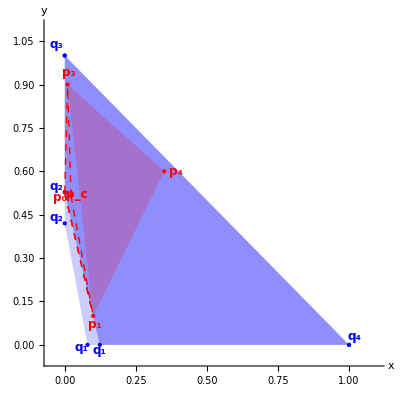

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of outer polygon Q1*)
q1Vertices={q11,q12,q3,q4};
q1Labels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw outer polygon Q1*)
Style[Polygon[q1Vertices],Opacity[0.3],Blue],
Blue,PointSize[Medium],Point[q1Vertices],

Red,
Point[p21],Text[Style[Subscript["p",c],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{0.02,0.005}],

Point[p20],Text[Style[Subscript["p",0],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.04,-0.005}],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],

Table[
Text[Style[q1Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q1Vertices[[i]]+If[i==1,{0,-0.02},{-0.03,0.02}]],{i,Length[q1Vertices]-2}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
 
Red, Line[{p20,p21}],
Dashed, Line[{p20,p1}], Line[{p20,p3}],Line[{p20,p1}],Line[{p21,p3}],Line[{p21,p1}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1,ImageSize->Full
]
```

## Biggest Q, smallest P

```mathematica
s1= s1 /.{b1->0}
```

(100601 x)/42007-(8727 (1-x-y))/42007+(12055 y)/42007

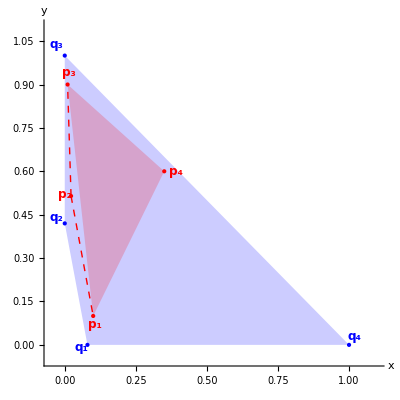

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],


(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1,ImageSize->Full
]
```

## Computations

### Algorithm for vertices of outer polytope

```mathematica
(*Vertex q1 *)
supportinglines = findSupportingLines[q01,p1,p21,p3,p4];

v1 = findIntersectionWithBoundary[supportinglines[[1]],s1,s2,s3,s4,ineqsQ0,q01];

v2 = findIntersectionWithBoundary[supportinglines[[2]],s1,s2,s3,s4,ineqsQ0,q01];

(* Convex hull of q1,v1,v2 *)

l1v1= line[q01,v1];
l1v2=line[q01,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p21,p3,p4]
```

False: This triangle is not nested between P and Q

False

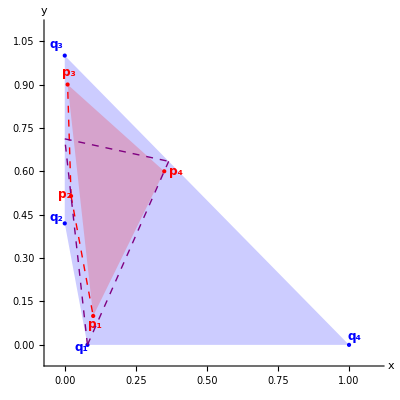

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{q01,v1}],Line[{q01,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1
]
```

```mathematica
(*Vertex q2 *)
supportinglines = findSupportingLines[q02,p1,p21,p3,p4];

v1 = findIntersectionWithBoundary[supportinglines[[1]],s1,s2,s3,s4,ineqsQ0,q02];

v2 = findIntersectionWithBoundary[supportinglines[[2]],s1,s2,s3,s4,ineqsQ0,q02];

(* Convex hull of q2,v1,v2 *)

l1v1= line[q02,v1];
l1v2=line[q02,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p21,p3,p4]
```

False: This triangle is not nested between P and Q

False

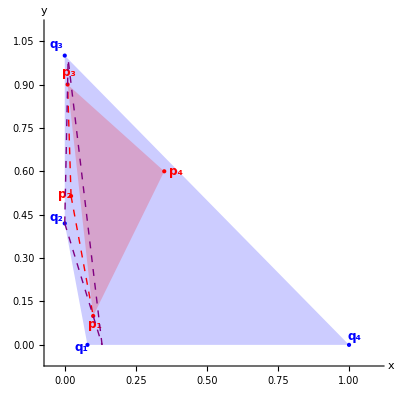

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{q02,v1}],Line[{q02,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1,ImageSize->Full
]
```

```mathematica
(*Vertex q3 *)
supportinglines = findSupportingLines[q3,p1,p21,p3,p4];

v1 = findIntersectionWithBoundary[supportinglines[[1]],s1,s2,s3,s4,ineqsQ0,q3];

v2 = findIntersectionWithBoundary[supportinglines[[2]],s1,s2,s3,s4,ineqsQ0,q3];

(* Convex hull of q3,v1,v2 *)

l1v1= line[q3,v1];
l1v2=line[q3,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p21,p3,p4]
```

False: This triangle is not nested between P and Q

False

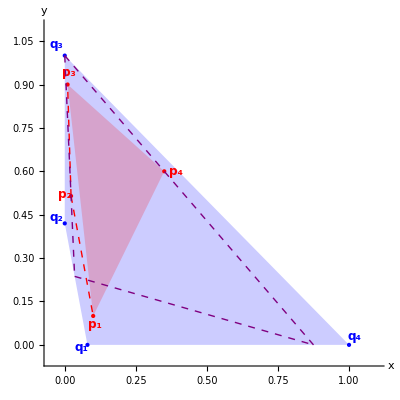

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{q3,v1}],Line[{q3,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1,ImageSize->Full
]
```

```mathematica
(*Vertex q4 *)
supportinglines = findSupportingLines[q4,p1,p21,p3,p4];

v1 = findIntersectionWithBoundary[supportinglines[[1]],s1,s2,s3,s4,ineqsQ0,q4];

v2 = findIntersectionWithBoundary[supportinglines[[2]],s1,s2,s3,s4,ineqsQ0,q4];

(* Convex hull of q4,v1,v2 *)

l1v1= line[q4,v1];
l1v2=line[q4,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p21,p3,p4]
```

False: This triangle is not nested between P and Q

False

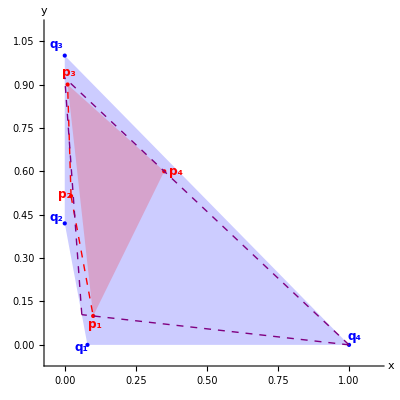

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{q4,v1}],Line[{q4,v2}], Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,1.1},{-0.05,1.1}},AspectRatio->1,ImageSize->Full
]
```

### Algorithm for edges of inner polytope

```mathematica
(*inner edge 12 *)
l12 = line[p21,p1];
v1 =point[l12, s2];
v2=point[l12, s3];

l1 = findSupportingVertex[v1,p3,p4, p1,p21,p3,p4];
l2 =  findSupportingVertex[v2,p3,p4, p1,p21,p3,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Reduce[ineqsQ0/.v3subs]
```

False

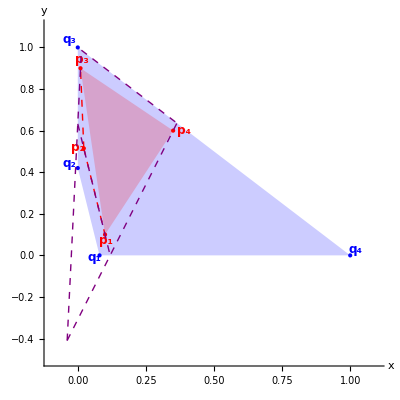

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{v3,{6151/464435,458284/464435}}],Line[{v3,{4854317/13339385,8485068/13339385}}], Line[{{6151/464435,458284/464435},{4854317/13339385,8485068/13339385}}],Line[{v1,v2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.1,1.1},{-0.5,1.1}},AspectRatio->1,ImageSize->Full
]
```

```mathematica
(*inner edge 23 *)
l23 = line[p21,p3];
v1 =point[l23, s1];
v2=point[l23, s4];

l1 = line[v1,p1];
l2 =  line[v2,p4];

v3 = point[l1,l2];

v3subs= {x->v3[[1]],y->v3[[2]]};
Reduce[ineqsQ0/.v3subs]
```

False

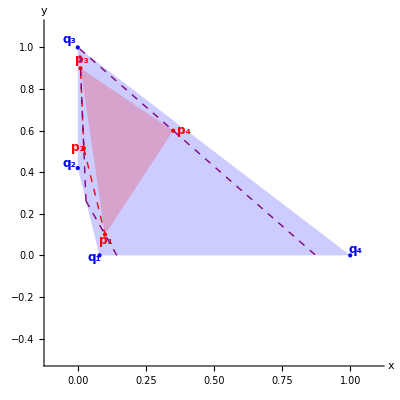

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{v1,v2}],Line[{v1,{854708889/5965707616,0}}],Line[{v2,{275447/315283,0}}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.1,1.1},{-0.5,1.1}},AspectRatio->1,ImageSize->Full
]
```

```mathematica
(*inner edge 34 *)
l34 = line[p4,p3];
v1 =point[l34, s2];
v2=point[l34, s4];

l1 = line[v1,p21];
l2 =  line[v2,p1];

v3 = point[l1,l2];

Reduce[ineqsQ0/.{x->v3[[1]],y->v3[[2]]}]
```

False

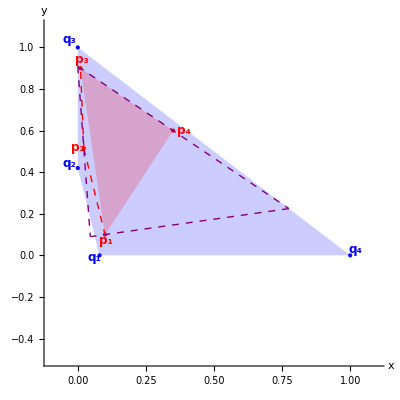

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{v1,v2}],Line[{v1,v3}],Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.1,1.1},{-0.5,1.1}},AspectRatio->1,ImageSize->Full
]
```

```mathematica
(*inner edge 14 *)
l14 = line[p4,p1];
v1 =point[l14, s1];
v2=point[l14, s4];

l1 = line[v1,p21];
l2 =  line[v2,p3];

v3 = point[l1,l2];

Reduce[ineqsQ0/.{x->v3[[1]],y->v3[[2]]}]
```

False

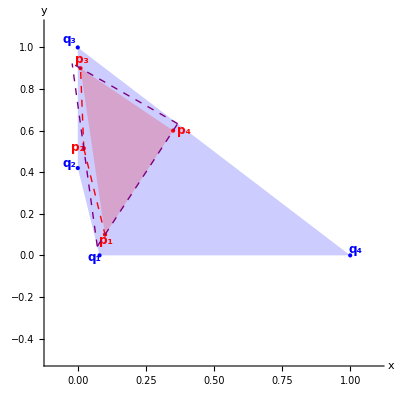

```mathematica
(*Vertices of outer polygon Q0*)
q0Vertices={q01,q02,q3,q4};
q0Labels={Subscript["q",01],Subscript["q",02],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p1,p3,p4};
pLabels={Subscript["p",1],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q0*)
Style[Polygon[q0Vertices],Opacity[0.2],Blue],
Blue,PointSize[Medium],Point[q0Vertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Medium],Point[pVertices],

Point[p21],Text[Style[Subscript["p",2],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p21+{-0.02,0.005}],
(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[q0Labels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
q0Vertices[[i]]+If[i==4,{0.02,0.03},If[i==1,{-0.02,-0.01},If[i==2,{-0.03,0.02},{-0.03,0.04}]]]],{i,Length[q0Vertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{0.005,-0.03},If[i==2,{0.005,0.04},{0.04,0}]] ],{i,Length[pVertices]}],
Dashed, Line[{p21,p1}], Line[{p21,p3}],
Purple,
Line[{v1,v2}],Line[{v1,v3}],Line[{v2,v3}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.1,1.1},{-0.5,1.1}},AspectRatio->1,ImageSize->Full
]
```